# Trivial Equilibria Stability Analysis

```mathematica
ClearAll[phi,psi,A,B,phiPrime,psiPrime,APrime,BPrime,dA,dB,p,b,m,s]

F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M={{dA*(1-B)+p*B,dA*A,0,0},{dB*B,dB*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}};
(*Vector on the right-hand side*)
RHS={-s*phi-F[A,B],-s*psi-G[A,B],phi,psi};
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
LHS=Inverse[M].RHS;
(*Solve for derivatives when {phi',psi',A',B'}=0*)
EquilibriaEquation = LHS == {0,0,0,0};
equilibria = Solve[EquilibriaEquation, {phi, psi, A, B}];
(*Returning the trivial equilibria(0,0,0,0)*)
trivialEquilibrium=equilibria [[1]];
(*Print the trivial equilibria*)
Print[trivialEquilibrium]
```

```mathematica
(*Find the Jacobian of the system *)
JacMatrix = D[LHS,{{phi,psi,A,B}}] ;
JacMatrixForm = JacMatrix // MatrixForm
ParamReplacements={D->0.1,p->0.2,dA->0.01, dB->0.01 ,m->0.001};
NumJacMatrix = JacMatrix /. paramReplacements;
```

(-((-A b-b B+dB-A dB) s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)) | (A dA s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)) | (A B dA (-2 b-2 p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((-A b-b B+dB-A dB) (dA-2 B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-((-A b-b B+dB-A dB) (-B dA dB+(-b-dB) ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2+((-b-dB) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(A dA (-B dA dB+(-b-dB) ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-(dA (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)) | ((-A b-b B+dB-A dB) (-m-2 A p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(A dA (-2 b+2 b B+2 b (A+B)+dB+m+2 A p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-((-A b-b B+dB-A dB) (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-(b (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(A dA (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2
(B dB s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)) | -((dA-B dA+B p) s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)) | -(B dB (dA-2 B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(B (-2 b-2 p) (dA-B dA+B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(B dB (-B dA dB+(-b-dB) ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-((dA-B dA+B p) (-B dA dB+(-b-dB) ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2 | -(B dB (-m-2 A p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((-2 b+2 b B+2 b (A+B)+dB+m+2 A p) (dA-B dA+B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(B dB (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-(dB (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-((dA-B dA+B p) (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2+((-dA+p) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
TrivialEqJacob = jacobianMatrix /. trivialEquilibrium
NumTrivialEqJac = NumJacMatrix /. trivialEquilibrium
```

{{-s/dA,0,1,-m/dA},{0,-s/dB,0,(-2 b+dB+m)/dB},{1,0,0,0},{0,1,0,0}}

{{-100. s,0.,1.,-0.1},{0.,-100. s,0.,0.+100. (0.011-2 b)},{1,0,0,0},{0,1,0,0}}

```mathematica
EigenTrivial = Eigenvalues[TrivialEqJacob]
NumEigenTrivial = Eigenvalues[NumTrivialEqJac]
```

{(-dB s-dB √(4 dA^2+s^2))/(2 dA dB),(-dB s+dB √(4 dA^2+s^2))/(2 dA dB),(-dA s-√(-8 b dA^2 dB+4 dA^2 dB^2+4 dA^2 dB m+dA^2 s^2))/(2 dA dB),(-dA s+√(-8 b dA^2 dB+4 dA^2 dB^2+4 dA^2 dB m+dA^2 s^2))/(2 dA dB)}

{1/2 (-100. s-√(4.+10000. s^2)),1/2 (-100. s+√(4.+10000. s^2)),1/2 (-100. s-√(4.4-800. b+10000. s^2)),1/2 (-100. s+√(4.4-800. b+10000. s^2))}

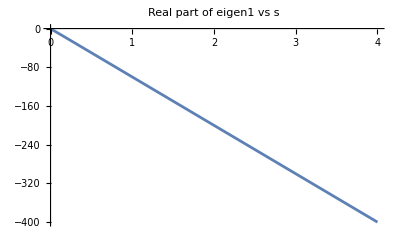

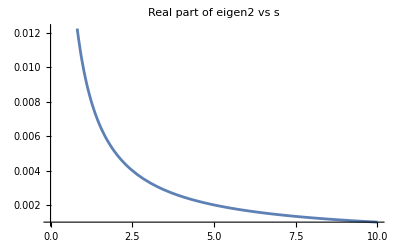

-Graphics3D-

-Graphics3D-

```mathematica
eigen1[b_,s_]:=(-100 s-Sqrt[4+10000 s^2])/2;
eigen2[b_,s_]:=(-100 s+Sqrt[4+10000 s^2])/2;
eigen3[b_,s_]:=(-100 s-Sqrt[4.4-800*b+10000 s^2])/2;
eigen4[b_,s_]:=(-100 s+Sqrt[4.4-800*b+10000 s^2])/2;

Plot[Re[eigen1[b,s]],{s,0,4},PlotLabel->"Real part of eigen1 vs s"]
Plot[Re[eigen2[b,s]],{s,0,10},PlotLabel->"Real part of eigen2 vs s"]
Plot3D[
 Re[eigen3[b, s]],
 {b, -1, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen3 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen3]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]

Plot3D[
 Re[eigen4[b, s]],
 {b, -1, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen4 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen4]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
```